```mathematica
Options[UpperDarbouxSum]={Subdivisions->10,Rectangles->True}
UpperDarbouxSum[f_,{a_,b_},OptionsPattern[]]:=Module[{n=OptionValue[Subdivisions],arr,arr2,sum,farr,int,plt},arr2=Subdivide[a,b,n];
int=Partition[Riffle[arr2[[;;-2]],arr2[[2;;]]],2];
farr=Map[MaxValue[{f[x],x≥#[[1]],x≤#[[2]]},x]&,int];
sum=Total[Map[MaxValue[{f[x],x≥#[[1]],x≤#[[2]]},x]&,int]*(Abs[b-a]/n)]//N;
If[OptionValue[Rectangles],plt=Show@@{Join[{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large}]},Table[Plot[farr[[i]],{x,int[[i,1]],int[[i,2]]},PlotStyle->{Blue},Filling->Axis],{i,Length[farr]}]],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large},plt=Show@@{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large}],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large}];
Return[{plt,sum}]]

Options[LowerDarbouxSum]={Subdivisions->10,Rectangles->True}
LowerDarbouxSum[f_,{a_,b_},OptionsPattern[]]:=Module[{n=OptionValue[Subdivisions],arr,arr2,sum,farr,int,plt},arr2=Subdivide[a,b,n];
int=Partition[Riffle[arr2[[;;-2]],arr2[[2;;]]],2];
farr=Map[MinValue[{f[x],x≥#[[1]],x≤#[[2]]},x]&,int];
sum=Total[Map[MinValue[{f[x],x≥#[[1]],x≤#[[2]]},x]&,int]*(Abs[b-a]/n)]//N;
If[OptionValue[Rectangles],plt=Show@@{Join[{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large},PlotRange->Full]},Table[Plot[farr[[i]],{x,int[[i,1]],int[[i,2]]},PlotStyle->{Blue},Filling->Axis],{i,Length[farr]}]],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large},plt=Show@@{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large},PlotRange->Full],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large}];
Return[{plt,sum}]]

Options[RiemanSum]={FunctionValues->Left,Subdivisions->10,Rectangles->True}
RiemanSum[f_,{a_,b_},OptionsPattern[]]:=Module[{n=OptionValue[Subdivisions],arr,arr2,sum,farr,int,plt},(*Print[n];*)If[OptionValue[FunctionValues]==Left,arr=Subdivide[a,b,n][[;;-2]]];
If[OptionValue[FunctionValues]==Right,arr=Subdivide[a,b,n][[2;;]]];
If[OptionValue[FunctionValues]==Center,arr=Range[a+(Abs[b-a]/n)/2,b,(Abs[b-a]/n)]];
farr=Map[f,arr];
arr2=Subdivide[a,b,n];
int=Partition[Riffle[arr2[[;;-2]],arr2[[2;;]]],2];
sum=N[Total[Map[f,arr]*(Abs[b-a]/n)],10];
If[OptionValue[Rectangles],plt=Show@@{Join[{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large},PlotRange->Full]},Table[Plot[farr[[i]],{x,int[[i,1]],int[[i,2]]},PlotStyle->{Blue},Filling->Axis],{i,Length[farr]}]],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large},plt=Show@@{Plot[f[x],{x,a,b},PlotStyle->{Black,Thickness->Large},PlotRange->Full],PlotRange->{{a,b},{MinValue[{f[x],x≥a,x≤b},x],MaxValue[{f[x],x≥a,x≤b},x]}},PlotLabel->"Сумма="<>ToString[sum],ImageSize->Large}];
Return[{plt,sum}]]
```

```mathematica
(*Часть 1*)
(*задание 1*)
```

```mathematica
f1[x_]:=Sqrt[1+x^3];
```

```mathematica
(*а*)
```

```mathematica
{plt11R, sum11R}=RiemanSum[f1,{0,1}, FunctionValues->Center, Subdivisions->5];
```

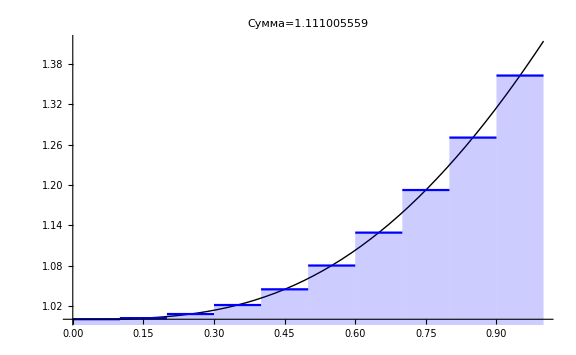
{-Graphics-,1.111005559}

```mathematica
{plt12R, sum12R}=RiemanSum[f1, {0,1}, FunctionValues->Center, Subdivisions->10]
```

```mathematica
Abs[sum11R-sum12R]≤0.001
```

False

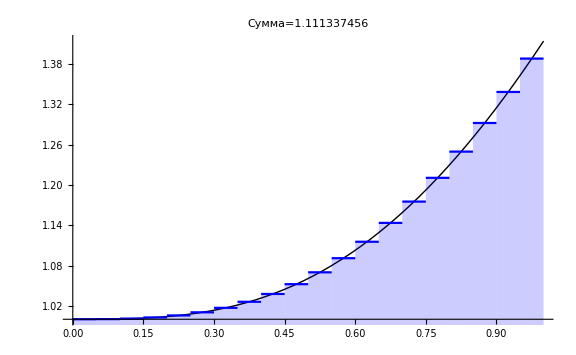
{-Graphics-,1.111337456}

```mathematica
{plt13R, sum13R}=RiemanSum[f1, {0,1}, FunctionValues->Center, Subdivisions->20]
```

```mathematica
Abs[sum13R-sum12R]≤0.001
```

True

```mathematica
(*подходит по точности разбиение от 10*)
```

```mathematica
(*б*)
```

```mathematica
{plt11LD, sum11LD} = LowerDarbouxSum[f1, {0,1}, Subdivisions->100];
```

```mathematica
{plt11UD, sum11UD} = UpperDarbouxSum[f1, {0,1}, Subdivisions->100];
```

```mathematica
sum11UD-sum11LD≤0.001
```

False

```mathematica
{plt12LD, sum12LD} = LowerDarbouxSum[f1, {0,1}, Subdivisions->200];
```

```mathematica
{plt12UD, sum12UD} = UpperDarbouxSum[f1, {0,1}, Subdivisions->200];
```

```mathematica
sum12UD-sum12LD≤0.001
```

False

```mathematica
{plt13LD, sum13LD} = LowerDarbouxSum[f1, {0,1}, Subdivisions->400, Rectangles->False];
```

```mathematica
{plt13UD, sum13UD} = UpperDarbouxSum[f1, {0,1}, Subdivisions->400, Rectangles->False];
```

```mathematica
sum13UD-sum13LD≤0.001
```

False

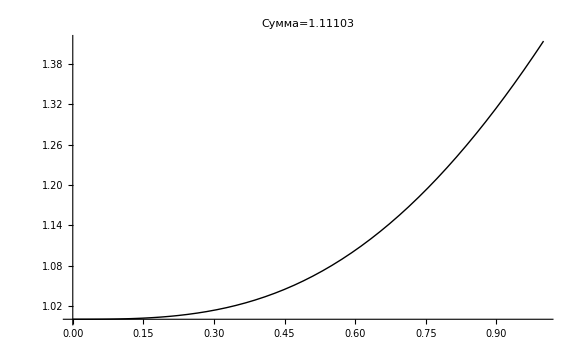
{-Graphics-,1.11103}

```mathematica
{plt14LD, sum14LD} = LowerDarbouxSum[f1, {0,1}, Subdivisions->500,Rectangles->False]
```

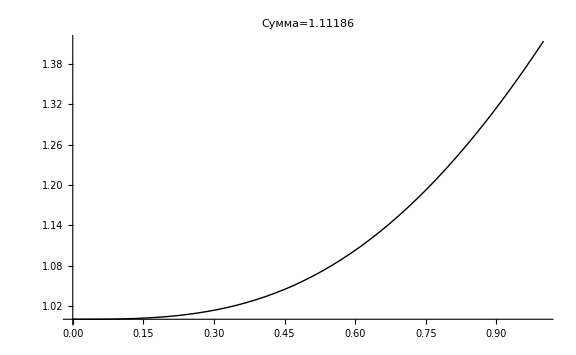
{-Graphics-,1.11186}

```mathematica
{plt14UD, sum14UD} = UpperDarbouxSum[f1, {0,1}, Subdivisions->500, Rectangles->False]
```

```mathematica
sum14UD-sum14LD≤0.001
```

True

```mathematica
(*подходит разбиение от 500*)
```

```mathematica
(*задание 2*)
```

```mathematica
f2[x_]:=1/(1+x^2)
```

```mathematica
(*а*)
```

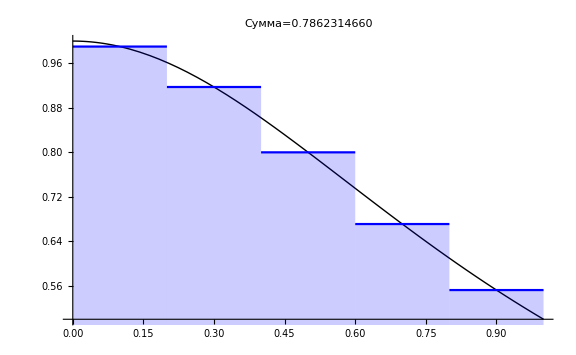
{-Graphics-,0.786231466}

```mathematica
{plt21R, sum21R}=RiemanSum[f2,{0,1}, FunctionValues->Center, Subdivisions->5]
```

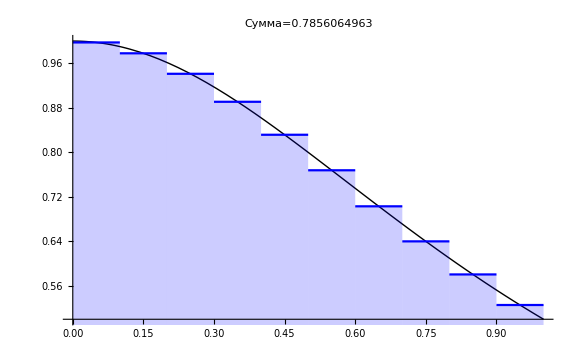
{-Graphics-,0.7856064963}

```mathematica
{plt22R, sum22R}=RiemanSum[f2,{0,1}, FunctionValues->Center, Subdivisions->10]
```

```mathematica
Abs[sum21R-sum22R]≤0.001
```

True

```mathematica
pi1 = sum21R*4
```

3.144925864

```mathematica
pi2 = sum22R*4
```

3.142425985

```mathematica
(*подходящая точность при разбиении от 5, точность пи до двух знаков*)
```

```mathematica
(*б*)
```

```mathematica
{plt21LD, sum21LD} = LowerDarbouxSum[f2, {0,1}, Subdivisions->100];
```

```mathematica
{plt21UD, sum21UD} = UpperDarbouxSum[f2, {0,1}, Subdivisions->100];
```

```mathematica
sum21UD-sum21LD≤0.001
```

False

```mathematica
{plt22LD, sum22LD} = LowerDarbouxSum[f2, {0,1}, Subdivisions->200, Rectangles->False];
```

```mathematica
{plt22UD, sum22UD} = UpperDarbouxSum[f2, {0,1}, Subdivisions->200, Rectangles->False];
```

```mathematica
sum22UD-sum22LD≤0.001
```

False

```mathematica
{plt23LD, sum23LD} = LowerDarbouxSum[f2, {0,1}, Subdivisions->400, Rectangles->False];
```

```mathematica
{plt23UD, sum23UD} = UpperDarbouxSum[f2, {0,1}, Subdivisions->400, Rectangles->False];
```

```mathematica
sum23UD-sum23LD≤0.001
```

False

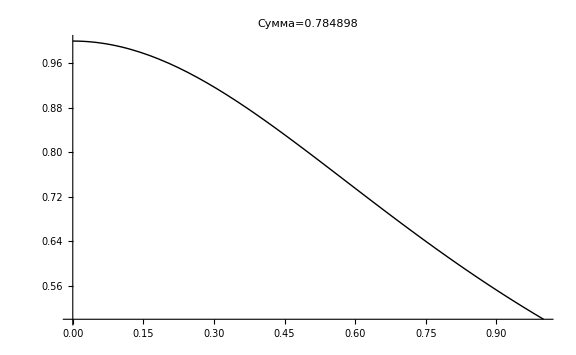
{-Graphics-,0.784898}

```mathematica
{plt24LD, sum24LD} = LowerDarbouxSum[f2, {0,1}, Subdivisions->500, Rectangles->False]
```

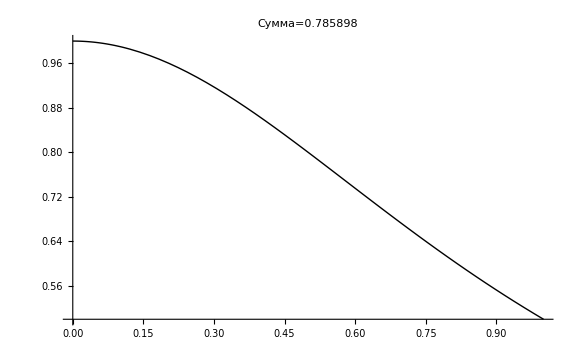
{-Graphics-,0.785898}

```mathematica
{plt24UD, sum24UD} = UpperDarbouxSum[f2, {0,1}, Subdivisions->500, Rectangles->False]
```

```mathematica
sum24UD-sum24LD≤0.001
```

True

```mathematica
pi3 = sum24LD*4
```

3.13959

```mathematica
pi4 = sum24UD*4
```

3.14359

```mathematica
(*подходящая точность при разбиении от 500, точность пи до двух знаков*)
```

```mathematica
(*Часть 2*)
```

```mathematica
(*задание 3*)
```

```mathematica
plt3= ContourPlot[{CubeRoot[x^2]+CubeRoot[y^2]==1, y^2==x^4}, {x, -1,1}, {y, -1,1}];
```

```mathematica
points3 = x/.Solve[x^4==(1-CubeRoot[x^2])^3 ]
```

{-√(-2+√5),√(-2+√5)}

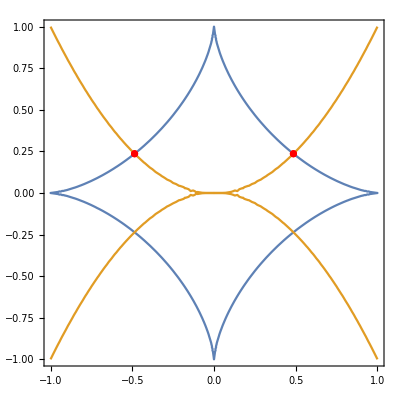

```mathematica
Show[plt3, ListPlot[{{points3[[2]],(points3[[2]])^2}}, PlotStyle->Red],ListPlot[{{points3[[1]],(points3[[1]])^2}}, PlotStyle->Red]]
```

```mathematica
sol31 = y/.Solve[y^2==x^4, y]
```

{-x^2,x^2}

```mathematica
f31[x_]:=sol3[[2]]
```

```mathematica
sol32=y/.Solve[y^2==(1-CubeRoot[x^2])^3, y]
```

{-√(1-x^2-3 (x^2)^(1/3)+3 ((x^2)^(1/3))^2),√(1-x^2-3 (x^2)^(1/3)+3 ((x^2)^(1/3))^2)}

```mathematica
f32[x_]:=sol32[[2]]
```

```mathematica
rightUpperLeftPart = NIntegrate[f31[x],{x, 0, points3[[2]]} ]
```

0.0382326

```mathematica
rightUpperRightPart = NIntegrate[f32[x],{x, points3[[2]], 1} ]
```

0.0460651

```mathematica
rightUpperPart = rightUpperLeftPart+rightUpperRightPart
```

0.0842977

```mathematica
(*мы нашли правый-верхний кусочек, так как график симметричен относительно осей х и у, общая сумма равна ему, умноженному на 4)
```

```mathematica
rightUpperPart*4
```

0.337191

```mathematica
(*ответ: площадь фигуры 0.3371908254901503*)
```

```mathematica
(*задание 4*)
```

```mathematica
plt4= ContourPlot[{5y^3==x^2, y^2+x^2==4}, {x, -2,2}, {y, -2,2}];
```

```mathematica
points4 = x/.Solve[CubeRoot[(x^2)/5]==Sqrt[4-x^2] ]
```

{AlgebraicNumber-1.80AlgebraicNumber[Root[-1000000+30000 #1^2-299 #1^4+#1^6&,2],{0,-1/5,0,0,0,0}]-1.802686659556939,AlgebraicNumber1.80AlgebraicNumber[Root[-1000000+30000 #1^2-299 #1^4+#1^6&,2],{0,1/5,0,0,0,0}]1.802686659556939}

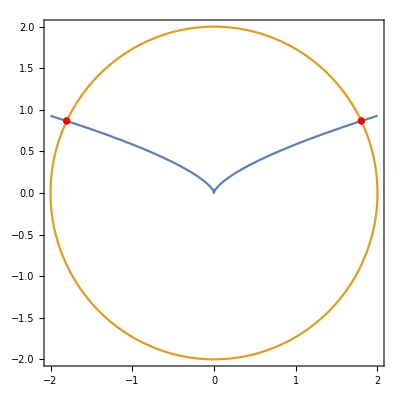

```mathematica
Show[plt4, ListPlot[{{points4[[2]],Sqrt[4-(points4[[2]])^2]}}, PlotStyle->Red],ListPlot[{{points4[[1]],Sqrt[4-(points4[[1]])^2]}}, PlotStyle->Red]]
```

```mathematica
sol41 = y/.Solve[y^2== 4-x^2, y]
```

{-√(4-x^2),√(4-x^2)}

```mathematica
f41[x_]:=sol41[[2]]
```

```mathematica
f42[x_]:=CubeRoot[(x^2)/5]
```

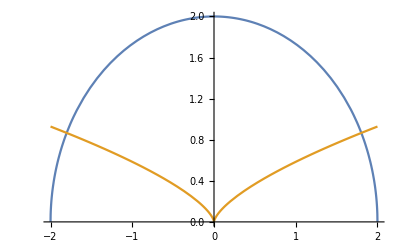

```mathematica
Plot[{f41[x], f42[x]}, {x, -2, 2}]
```

```mathematica
NIntegrate[f41[x]-f42[x], {x, points4[[1]], points4[[2]]}]
```

4.17914

```mathematica
(*ответ 4.179143531342035*)
```

```mathematica
(*задание 5*)
```

```mathematica
plt5= ContourPlot[{ x^2-y^2==x^4}, {x, -1,1}, {y, -1,1}];
```

```mathematica
sol5 = y/.Solve[x^2-y^2==x^4, y]
```

{-√(x^2-x^4),√(x^2-x^4)}

```mathematica
f51[x_]:=sol5[[1]]
```

```mathematica
f52[x_]:=sol5[[2]]
```

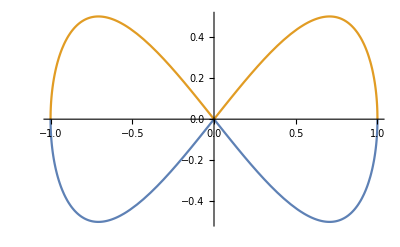

```mathematica
Plot[{f51[x],f52[x]}, {x, -1, 1}]
```

```mathematica
NIntegrate[f52[x]-f51[x], {x, -1, 1}]
```

1.33333

```mathematica
(*ответ 1.3333333333333703*)
```

```mathematica
(*задание 6*)
```

```mathematica
plt6= ContourPlot[{ 16x^4-16x^2==-y^2, y(1+x^2)==1}, {x, -2,2}, {y, -2,2}];
```

```mathematica
sol61 = y/.Solve[16x^4-16x^2==-y^2, y]
```

{-4 √(x^2-x^4),4 √(x^2-x^4)}

```mathematica
f61[x_]:=sol61[[2]]
```

```mathematica
f62[x_]:=1/(1+x^2)
```

```mathematica
points6 = x/.Solve[f61[x]==f62[x], x ];
```

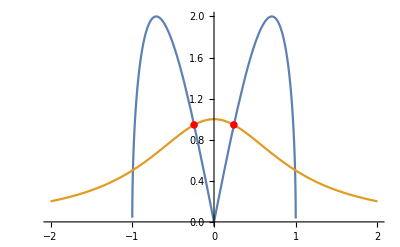

```mathematica
Show[Plot[{f61[x], f62[x]}, {x, -2,2}],ListPlot[{{points6[[2]],1/(1+(points6[[2]])^2)}}, PlotStyle->Red], ListPlot[{{points6[[1]],1/(1+(points6[[1]])^2)}}, PlotStyle->Red]]
```

```mathematica
NIntegrate[f62[x]-f61[x], {x, points6[[1]], points6[[2]]}]
```

0.244086

```mathematica
(*ответ 0.2440856581668183*)
```

```mathematica
(*задание 7*)
```

```mathematica
plt7= ContourPlot[{ x^3(1-x)==y^2,y^2==(x^3)/8}, {x, 0,1}, {y, -0.5,0.5}];
```

```mathematica
sol71 = y/.Solve[x^3(1-x)==y^2, y]
```

{-√(x^3-x^4),√(x^3-x^4)}

```mathematica
f71[x_]:=sol71[[2]]
```

```mathematica
sol72 = y/.Solve[y^2==(x^3)/8, y]
```

{-x^(3/2)/(2 √2),x^(3/2)/(2 √2)}

```mathematica
f72[x_]:=sol72[[2]]
```

```mathematica
points7= x/.Solve[f71[x]==f72[x], x ]
```

{0,7/8}

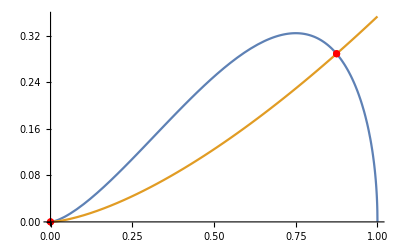

```mathematica
Show[Plot[{f71[x], f72[x]}, {x, 0,1}],ListPlot[{{points7[[2]],Sqrt[((points7[[2]])^3)/8]}}, PlotStyle->Red], ListPlot[{{points7[[1]],Sqrt[((points7[[1]])^3)/8]}}, PlotStyle->Red]]
```

```mathematica
upperPart = NIntegrate[f71[x]-f72[x], {x, points7[[1]], points7[[2]]}]
```

0.0688434

```mathematica
(*так как график симметричен относительно оси ОХ, площадь двух областей равна удвоенной площади верхней области*)
```

```mathematica
upperPart*2
```

0.137687

```mathematica
(*ответ 0.13768684107174745*)
```

```mathematica
(*задание 8*)
```

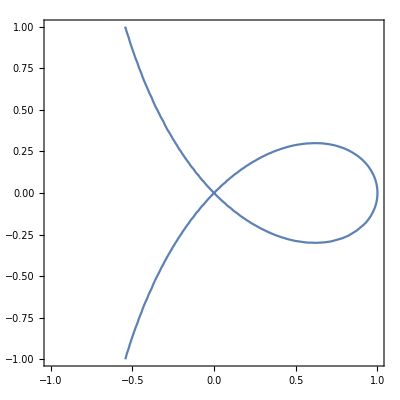

```mathematica
plt8= ContourPlot[y^2(1+x)==x^2(1-x), {x, -1,1}, {y, -1,1}]
```

```mathematica
sol8= y/.Solve[y^2(1+x)==x^2(1-x), y]
```

{-(√(x^2-x^3))/(√(1+x)),(√(x^2-x^3))/(√(1+x))}

```mathematica
f81[x_]:=sol8[[1]]
```

```mathematica
f82[x_]:=sol8[[2]]
```

```mathematica
points8=x/.Solve[f81[x]==f82[x], x ]
```

{0,1}

```mathematica
Show[Plot[{f81[x], f82[x]}, {x, -1,1}],ListPlot[{{points8[[2]],Sqrt[((points8[[2]])^3)/8]}}, PlotStyle->Red], ListPlot[{{points8[[1]],Sqrt[((points8[[1]])^3)/8]}}, PlotStyle->Red]]
```

```mathematica
NIntegrate[f82[x]-f81[x], {x, 0, 1}]
```

0.429204

```mathematica
(*ответ 0.4292036732051115*)
```